# Evaluation

BX Pan
2017.9.18

There was some variability depending on the geo-graphical area. For instance, over Europe, the anomaly correlations decreased much quicker than over the Northern Hemisphere extratropics as a whole.

Miyakoda et al. (1986) used a 10-day running mean for both the forecasts and the observed data in an attempt to obtain positive skills by filtering out the unpredictable components, most especially the baroclinic eddies

“They were in effect arguing about artifacts induced by sampling at too low a resolution.”

phase shifts

## Evaluation

Deterministic Scores

Time Scale

Daily

Weekly

Spatial Scale

Grid

Area Average

Correlation Coefficient(r^2) and Root Mean Square Error(RMSE) are probably not the most suitable for assessing probabilistic forecasts after 10 days, but they are the most widely used for evaluating medium-range weather forecasting and they were used in previous papers on monthly forecasting. It should be Beat Climatology and Persistence (Molteni et al., 1986).

Example: BoM Dataset

#### Sample Collection

The Oct to Feb hindcasts for the West Coast CONUS were gathered as follows. Together there are 161 boreal winter months(33 years).

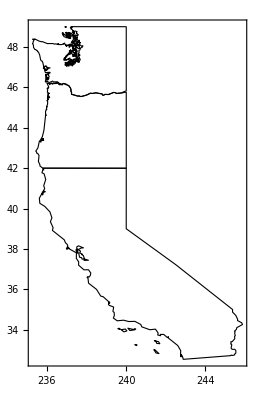

```mathematica
polygon=Block[{westconus},
	westconus=Block[{ow,ca},
	ow=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/oregonwashington.mx"];
	ca=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/california.mx"];
	Polygon[Flatten[{ow[[1]],ca[[1]]},1]]];
	westconus[[1]]];
(*polygon in the form of {subpoly1,subpoly2,...},subpoly in th form of {{long1,lat1},{long2,lat2}...}*)
Graphics[{EdgeForm[Black],FaceForm[None],westconus},Frame->True]
```

```mathematica
CollectSamples[dataname_,polygon_]:=Block[{dataset,data},
	dataset=Block[{},
		SetDirectory["/Users/lambda/Documents/Data/S2S/"<>dataname];
		Map["/Users/lambda/Documents/Data/S2S/"<>dataname<>"/"<>#&,
			Flatten[Table[FileNames["*-"<>month<>"-*.nc"],{month,{"01","02","10","11","12"}}]]]];
    data=Block[{origin=Map[S2SCut[polygon,#]&,dataset],position},
		position=Position[origin, _?(# <-1.0 &)];
		Map[If[Length[#]==4,Set[origin[[#[[1]],#[[2]],#[[3]],#[[4]]]],0.0],
		    If[Length[#]==5,Set[origin[[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]]],0.0],
			If[Length[#]==3,Set[origin[[#[[1]],#[[2]],#[[3]]]],0.0]]]]&,position];
		origin];
	Export["/Users/lambda/Documents/Data/S2S/"<>dataname<>"/"<>dataname<>"_WestCONUS.mx",data];
	data];
```

```mathematica
SetDirectory["/Users/lambda/Documents/Data/S2S/"];
datanames=FileNames[][[{1,2,4,5,6,7,8,9,10,11,12}]];
TableForm[Map[Block[{tempt=Import["/Users/lambda/Documents/Data/S2S/"<>#<>"/"<>#<>"_WestCONUS.mx"]},
	Flatten[{#,Dimensions[tempt[[;;,2]]]}]]&,datanames],
	TableHeadings->{None, {"Name","Months","Grids","Length","EnsembleSize"}},
	TableAlignments->Center]
```

Name | Months | Grids | Length | EnsembleSize
BoM | 161 | 13 | 62 | 32
CMA | 105 | 33 | 60 | 3
ECCC | 100 | 33 | 32 | 3
ECMWF | 97 | 33 | 46 | 10
HCMR | 130 | 33 | 62 | 9
ISACCNR | 150 | 33 | 31 | 1
JMA | 150 | 33 | 34 | 4
KMA | 80 | 33 | 60 | 2
MeteoFrance | 105 | 33 | 61 | 14
NCEP | 60 | 33 | 44 | 3
UKMO | 115 | 33 | 60 | 2

## Evaluation

```mathematica
dataset="ECMWF";
simu=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_mix2.mx"];
points=Position[simu,_?(#<-0.0&)];
Map[Set[simu[[#[[1]],#[[2]],#[[3]],#[[4]]]],0.0]&,points];

obser=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_cpc.mx"];
points=Position[obser,_?(#<-0.0&)];
Map[Set[obser[[#[[1]],#[[2]],#[[3]]]],0.0]&,points];
```

```mathematica
PDFDraw[data_]:=Block[{𝒟},
	𝒟 = SmoothKernelDistribution[data];
	Plot[PDF[𝒟, x], {x, Min[data], Max[data]},PlotRange->Full]]
```

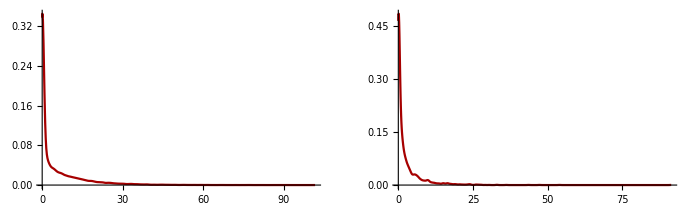

```mathematica
day=45;
grid=3;
GraphicsRow[{PDFDraw[Flatten[simu[[;;,day,grid,;;]]]],
		     PDFDraw[obser[[;;,day,grid]]]}]
```

```mathematica
Dimensions[simu]
Dimensions[obser]
MinMax[simu]
MinMax[obser]
```

{2962,46,33,11}

{2962,46,33}

{0.,194.76}

{0.,109.076}

```mathematica
RMSE[simu_,obser_]:=Sqrt[Mean[(simu-obser)^2]]
```

```mathematica
Scoring[dataset_,score_]:=Block[{simu,points,obser,test},
	simu=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_mix2.mx"];
	points=Position[simu,_?(#<-1.0&)];
	Map[Set[simu[[#[[1]],#[[2]],#[[3]],#[[4]]]],0.0]&,points];

	obser=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>"_cpc.mx"];
	points=Position[obser,_?(#<-1.0&)];
	Map[Set[obser[[#[[1]],#[[2]],#[[3]]]],0.0]&,points];
	
	test=Table[Table[Table[score[simu[[;;,t,grid,ensemble]],obser[[;;,t,grid]]],
	{ensemble,Dimensions[simu][[-1]]}],{grid,Dimensions[simu][[-2]]}],{t,Dimensions[simu][[-3]]}];
	
	Table[ListLinePlot[Table[test[[;;,j,i]],{i,Dimensions[test][[-1]]}],
	PlotStyle->Table[{Dashed,Gray},{i,Dimensions[test][[-1]]}],
	PlotRange->Full],{j,Dimensions[test][[-2]]}]]
```

```mathematica
Scoring["ECMWF",RMSE]
```

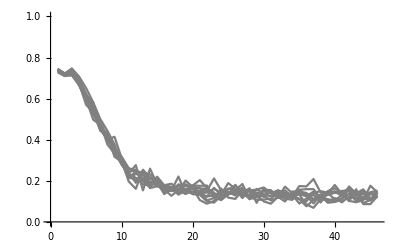
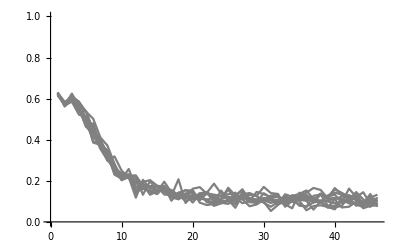
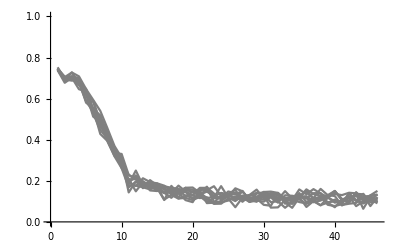
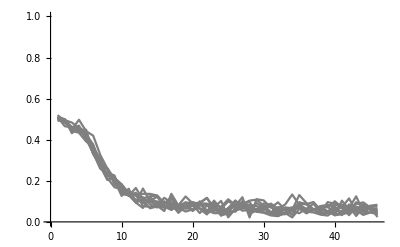
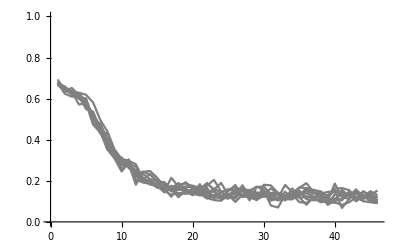
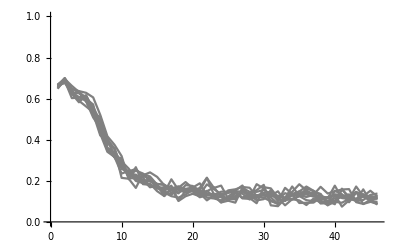
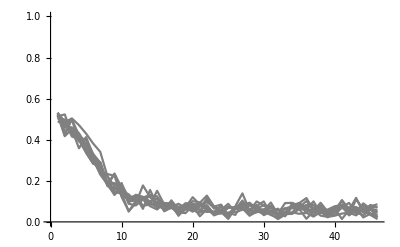
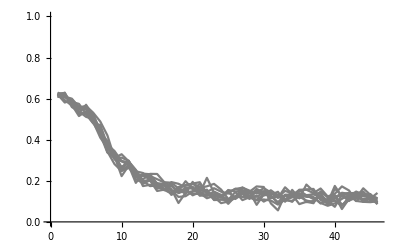
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Scoring["ECMWF",Correlation]
```

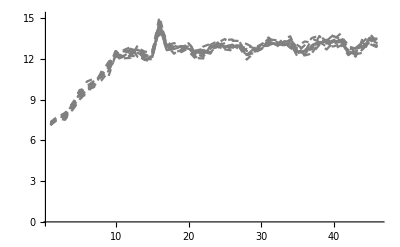
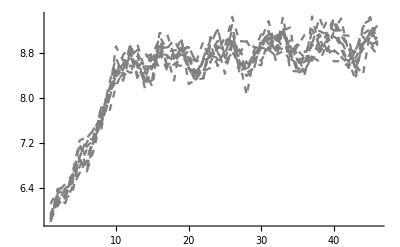
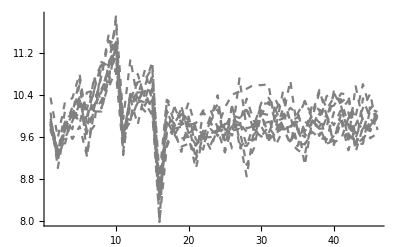
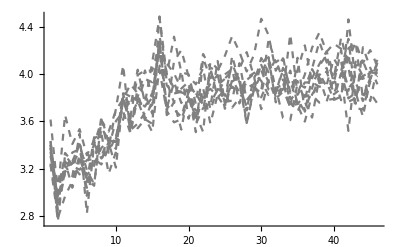
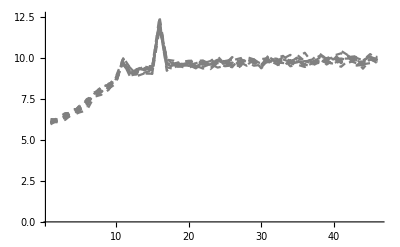
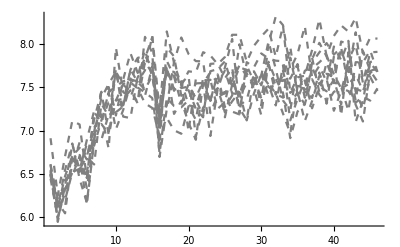
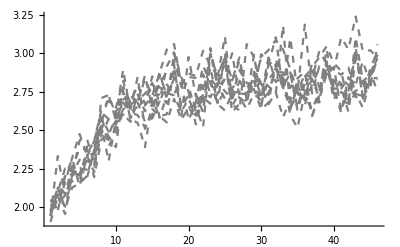
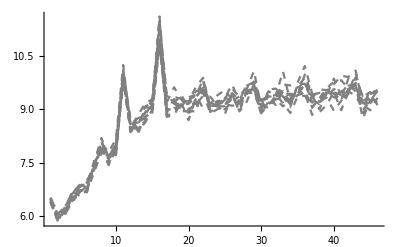

```mathematica
Scoring["NCEP",RMSE]
```

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

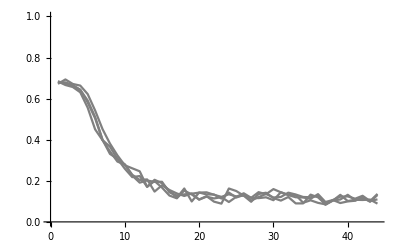
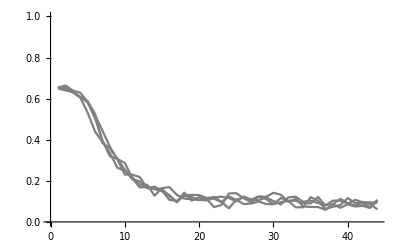
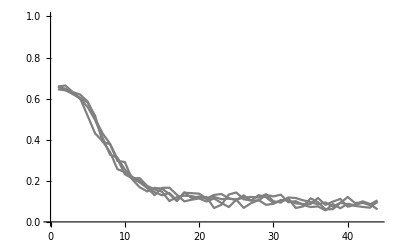
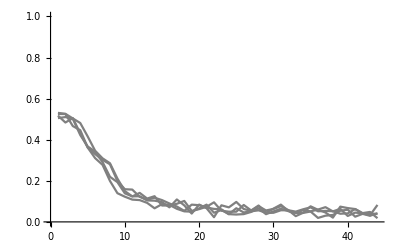
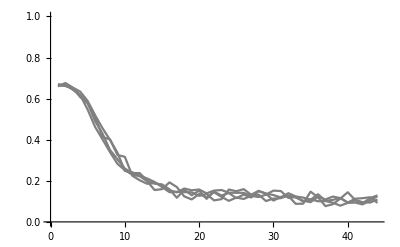
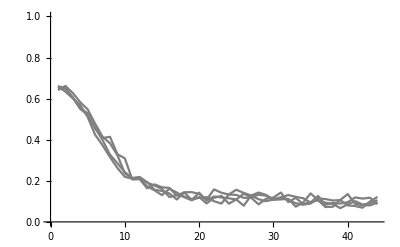
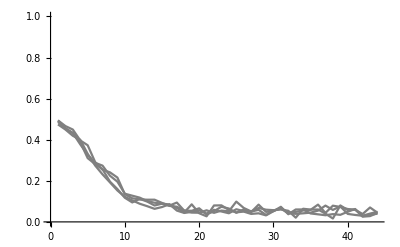
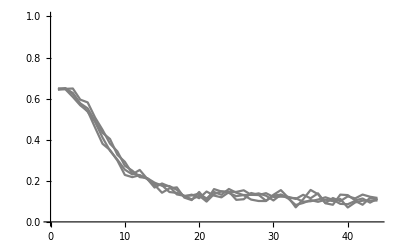
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Scoring["NCEP",Correlation]
```

```mathematica
Scoring["UKMO",RMSE]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### ReArrange

```mathematica
data=Block[{name="NCEP"},
	Import["/Users/lambda/Documents/Data/S2S/"<>name<>"/"<>name<>"_WestCONUS.mx"]];
```

```mathematica
SkillSequence[data_,score_]:=Block[{observation,simulation,size,grids,length,tempt,ensemble,Pmean,Pensemble},
	{size,tempt,grids,length}=Dimensions[data];
	ensemble=Dimensions[data[[1,2]]][[-1]];
	Pensemble=Table[Table[Table[score[data[[;;,1,grid,day]],data[[;;,2,grid,day,member]]],{day,length}],
		{grid,grids}],{member,ensemble}];
	Pmean=Table[Table[score[data[[;;,1,grid,day]],Map[Mean,data[[;;,2,grid,day]]]],{day,length}],{grid,grids}];
	{Pensemble,Pmean}];
```

```mathematica
RMSE[simu_,obser_]:=Sqrt[Mean[(simu-obser)^2.]];
score=Correlation;
{Pensemble,Pmean}=SkillSequence[data,score];
```

```mathematica
grid=8;
Show[{ListLinePlot[Pensemble[[;;,grid,;;]],PlotRange->{-0.2,0.9},PlotStyle->Table[{Gray,Dashed},Length[Pensemble]]],
ListLinePlot[Pmean[[grid,;;]],PlotStyle->{Thickness->0.015,Black}]},
Frame->True,
BaseStyle->20,
PlotLabel->"NCEP Forecast",
FrameLabel->{"Day",ToString[score]}]
```

-Graphics-

Probabilistic Scores

#### Relative Operating Characteristics (ROC) Scores

The relative operating characteristics (ROC) scores are based on contingency tables giving the number of observed occurrences and nonoccurrences of an event as a function of the forecast occurrences and nonoccurrences of that event. The events are defined as binary, for instance, the probability that 2-m temperature is in the upper tercile. (Stanski et al. 1989; Mason and Graham 1999; Kharin and Zwiers 2003)

For each parameter value θi the point TPR (θi), FPR (θi) is plotted; points corresponding to consecutive θi' s are connected with a line. We call the obtained curve the ROC curve for the classifier in consideration. The ROC curve resides in the ROC space as defined by the functions FPR and TPR corresponding respectively to the x - axis and the y - axis.

#### Brier Skill Scores

#### Continuous Ranked Probability Skill Score

#### Reliability diagrams

#### Rank Histograms

#### Kullback-Leibler divergence

#### Taylor diagram

## History of Attempts

```mathematica
Tuples[{1, 2}, 2]
```

{{1,1},{1,2},{2,1},{2,2}}

```mathematica
Rotate[Show[{RectangleChart[{{1,1},{1,2},{2,1},{2,-5},{1,-3}},
ChartElementFunction -> "GlassRectangle", ChartStyle -> "Pastel"],
	  RectangleChart[{{1,-1},{2,-4},{2,5},{1,3}}, 
	  ChartElementFunction -> "GlassRectangle", 
	  ChartStyle -> "Pastel"]},Axes->False],Pi/2]
```

-Graphics-

```mathematica
BarChart[Range[6], ChartElementFunction -> "GlassRectangle", 
ChartStyle -> "Pastel"]
```

-Graphics-

-Graphics-

```mathematica
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"]
FileNames[]
```

/Users/lambda/Documents/Research/S2SEvaluation/Data

{BoM_p,CMA_cp,.DS_Store,.DS_Store_control_time.mx,.DS_Store_control_time.mx_pertubation_time.mx,.DS_Store_control_time.mx_pertubation_time.mx_pertubation_time.mx,.DS_Store_pertubation_time.mx,.DS_Store_pertubation_time.mx_pertubation_time.mx,ECCC,ECMWF,HCMR_p,ISACCNR,JMA,KMA,MeteoFrance,NCEP,.tempt.sh.swp,UKMO}

```mathematica
dataset="UKMO";
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset];
control=Import["*_control.mx"];
pertubation=Import["*_pertubation.mx"];
If[Dimensions[control][[2]]==Dimensions[pertubation][[2]],
data=Table[Table[Table[Prepend[pertubation[[1,k,i,j]],control[[1,k,i,j]]],{j,Dimensions[control][[-1]]}],
	{i,Dimensions[control][[-2]]}],
	{k,Dimensions[control][[-3]]}];
Export[dataset<>"_mix.mx",data],dataset]
```

UKMO_mix.mx

```mathematica
ReScale[dataset_]:=Block[{data},
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset];
data=Import["*_mix.mx"][[1]];
data=Transpose[Table[If[i==1,data[[;;,;;,1,;;]],data[[;;,;;,i,;;]]-data[[;;,;;,i-1,;;]]],{i,Dimensions[data][[-2]]}]];
Export[dataset<>"_mix2.mx",data]]
```

```mathematica
Map[ReScale,{"ECCC","ECMWF","JMA","KMA","MeteoFrance","NCEP"}]
```

{ECCC_mix2.mx,ECMWF_mix2.mx,JMA_mix2.mx,KMA_mix2.mx,MeteoFrance_mix2.mx,NCEP_mix2.mx}

```mathematica
data=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/ECCC/ECCC_mix2.mx"];
```

```mathematica
Dimensions[data]
```

{2962,46,33,11}

```mathematica
MinMax[data]
```

{-0.0666085,276.876}

```mathematica
Dimensions[data]
```

{1780,32,33,4}

```mathematica
ListLinePlot[Transpose[data[[13,;;,3,;;]]],PlotRange->Full]
```

-Graphics-